```mathematica
a=3
```

3

```mathematica
b=1
```

1

```mathematica
x[t_]:=a*Cos[t]+(b*Cos[t])/(√(b^2*Cos[t]^2+a^2*Sin[t]^2))
```

```mathematica
y[t_]:=b*Sin[t]+(a*Sin[t])/(√(b^2*Cos[t]^2+a^2*Sin[t]^2))
```

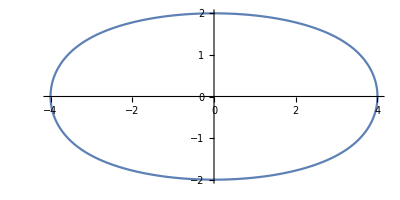

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,2π}]
```

```mathematica
NumberForm[NIntegrate[x[t]*(x[t]*y'[t]-x'[t]*y[t]),{t,0,π/2}]*4*π/3-4/3*π*a^2*b,11]
```

103.37870096